#### 2.1 | Gompertz Equation

```mathematica
Quit[]
```

Variable Selection

```mathematica
q0=5;p0=3;k=7;α=2;β=2;u=3;d=0.6;
```

```mathematica
p[t_]:= p0*Exp[Log[k/p0]*(1-Exp[-α*t])]
```

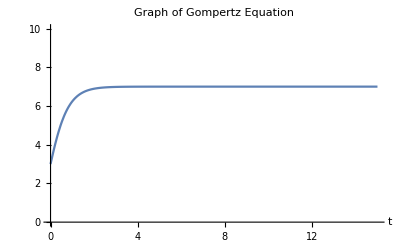

```mathematica
Plot[p[t],{t,0,15},PlotRange->{0,10},PlotLabel->"Graph of Gompertz Equation",AxesLabel->Automatic]
```